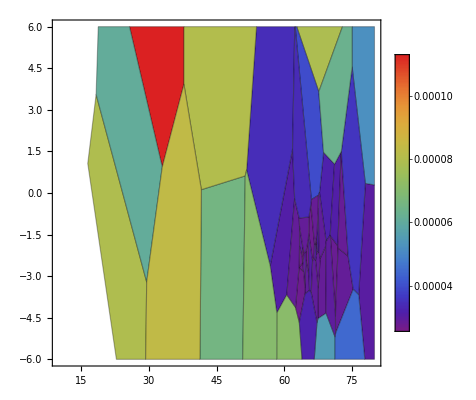

```mathematica
raw = Import["/Users/nmajik/Documents/SLAC/slacsyncgit/bmadExample/output_data.csv"];
raw[[1]];raw=raw[[2;;,{1,2,4}]];
ListDensityPlot[raw,ColorFunction->"Rainbow",InterpolationOrder->0,PlotLegends->Automatic,Mesh->All]
```

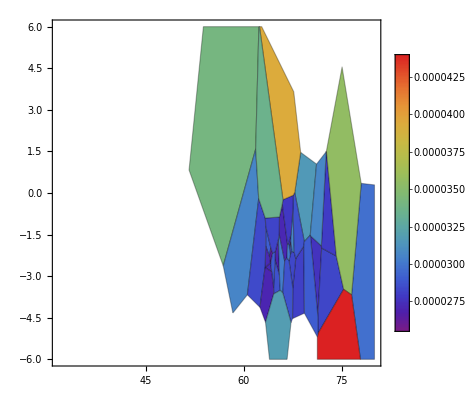

```mathematica
ListDensityPlot[raw,ColorFunction->"Rainbow",InterpolationOrder->0,PlotLegends->Automatic,PlotRange->{All,50*^-6},Mesh->All]
```